# .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00 .00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00z.01.00.00.8c.00.00.00.00.00.00

#### .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

```mathematica
ħ=1.054571817*^-34;(*J·s*)
ℏ=1.054571817*^-34;
e=1.602176634*^-19;(*C*)
ε0=8.8541878128*^-12;(*F·m⁻.b9*)
kB=1.380649*^-23; (*J·K^-1*)
εr=12.8;(*GaAs dielectric constant*)
nr=√εr;
m₀=9.1093837015*^-31;(*kg*)
mₑ=0.067 m₀;
mₕ=0.45 m₀;
c0=2.99792458*^8;(*m/s,speed of light in vacuum*)

rB=(4 π ε0 εr ħ^2)/(mₑ e^2);(* ~10.2 nm for GaAs*)
ER=ħ^2/(2 mₑ rB^2);(* ~5.8 meV "electron Rydberg:"*)

Eg=1.424*e/ER;(*dimensionless gap in effective Rydbergs at 300 K*)
Ep=28.8*e/ER;(*dimensionless Kane energy in effective Rydbergs at 300 K*)

a=5;(*a in units rB*)
c=0.5;(*c in units rB*)
δ=0.01;(*softening length*)

w[a_, c_][r_]:=c √(1-r^2/a^2);
ε[c_]:=π^2/c^2 ;
ω0[a_, c_]:=(2π)/(a c);
```

```mathematica
.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00z.01.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.07\[DownQuestion].a63.00.00.00A.18.8b\[Micro]\[UAcute].7f.00.00.19.00.00.00.00.00.00.00\[EAcute].1a\[EGrave].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00.00.00.00.00.00.00.00.00.00
```

.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00z.01.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.07\[DownQuestion].a63.00.00.00A.18.8b\[Micro]\[UAcute].7f.00.00.19.00.00.00.00.00.00.00\[EAcute].1a\[EGrave].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00.00.00.00.00.00.00.00.00.00.00

### .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

```mathematica
.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01
```

## .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00 .00.00.00.00.00.00.00.04.00

### .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00

```mathematica
.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00z.01.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.07\[DownQuestion].a63.00.00.00A.18.8b\[Micro]\[UAcute].7f.00.00.19.00.00.00.00.00.00.00\[EAcute].1a\[EGrave].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00.00.00.00.00.00.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[AGrave].b4\[UAcute].7f.00.00\[CapitalOSlash]m5\[Micro]\[UAcute].7f.00.00.8f>.8a\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.80.00.00.00.00.00.00.00.0e.00.00.00\[UAcute].7f.00.00.11.85=?\[ODoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEAcute]\[IDoubleDot]ce\[CapitalIDoubleDot].be.00.00.00.00.00.00z.01.00.00.01U.00.00.00.00.00.00.00.00.00.00.00.00.00.00p	\[DownQuestion].a63.00.00.00\[ADoubleDot].94\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00Z.02.00.00.00.00.00.00.80{.11(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.8f>.8a\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00p	\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.0e.00.00.00.00.00.00.00#.96\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.19\[AGrave]ce\[CapitalIDoubleDot].be.00.00.06.00.00.00.00.00.00.00DU.00.00.00.00.00.00.00.00.00.00.00.00.00.00@
\[DownQuestion].a63.00.00.00\[ADoubleDot].94\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.06.00.00.00z.01.00.00.00.00.00.00.00.00.00.00p.9a\[CCedilla]hz.01.00.00p.9a\[CCedilla]hz.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00(.94\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00@
\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00#.96\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00@
\[DownQuestion].a63.00.00.00\[CapitalEAcute]i\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00@
\[DownQuestion].a63.00.00.00.10.9d.92$z.01.00.00Si\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00\[CapitalEth].81\[DownQuestion].a63.00.00.00\[CCedilla]h\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00@
\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00]v\[CapitalIHat]\[Micro]\[UAcute].7f.00.00.06.00.00.00z.01.00.00\\[AAcute].95?\[ODoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[UDoubleDot]\[Thorn]Fiz.01.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80{.11(z.01.00.00\[UHat]\[AGrave]\[CapitalCCedilla]\[Micro]\[UAcute].7f.00.00.00.00\[SZ]^z.01.00.00.00.00.00.00z.01.00.00.80{.11(z.01.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.94P=?\[ODoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth].81\[DownQuestion].a63.00.00.00.80{.11(z.01.00.00.00.00.00.00.00.00.00.00.8e\[SZ].81?\[ODoubleDot].7f.00.00`/.11(z.01.00.00`/.11(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.94\[YDoubleDot]'z.01.00.00.00H.14(z.01.00.00\[CapitalEGrave].0f\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00.00.01.01.00.01.01.00.00.00.10.00.00.00.00.00.00.804.11(z.01.00.00.00.00.00.00.00.00.00.00\[CapitalEth].81\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000	.0f%z.01.00.00`.11\[DownQuestion].a63.00.00.00.80F.14(z.01.00.00.00.00.00.00.00.00.00.000~>\[Micro]\[UAcute].7f.00.00@~>\[Micro]\[UAcute].7f.00.00\[DoubleDot].8dN\[Micro]\[UAcute].7f.00.00\[CapitalARing]W\[CapitalUDoubleDot].b4\[UAcute].7f.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00zG.14(z.01.00.00.02.00.00.00\[UAcute].7f.00.000~>\[Micro]\[UAcute].7f.00.00@.0c\[DownQuestion].a63.00.00.00.01.00.00.00\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.18\[YAcute]-ckG.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00x\[Thorn]-ckG.00.00\[Paragraph]2.94\[Micro]\[UAcute].7f.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00\[IDoubleDot].be.00.00.00.00.00.00\[AGrave].0f\[DownQuestion].a63.00.00.00.88.17\[DownQuestion].a63.00.00.00.88.17\[DownQuestion].a63.00.00.00.01.00.00.00.00.00.00.00\[UAcute]H.14(z.01.00.00.00.00.00.00.00.00.00.00\[CapitalAHat]\[OTilde].06\[Micro]\[UAcute].7f.00.00.00H.14(z.01.00.00`.11\[DownQuestion].a63.00.00.00\[NonBreakingSpace].8dN\[Micro]\[UAcute].7f.00.00\[CapitalEDoubleDot]\[CapitalIGrave].06\[Micro]\[UAcute].7f.00.00x.0c\[DownQuestion].a63.00.00.00.01.00.00.00\[UAcute].7f.00.00.03.00.00.00z.01.00.00.00.00.00.00z.01.00.00.00Z\[IDoubleDot]^z.01.00.00.00.00.00.00.02.00.00.00x\[UAcute]-ckG.00.00@.01.00.00.00.00.00.00\[NonBreakingSpace].8dN\[Micro]\[UAcute].7f.00.00\[OHat].02.07\[Micro]\[UAcute].7f.00.00@.80\[IDoubleDot]^z.01.00.00.01H.14(z.01.00.00\[NonBreakingSpace]H.14(z.01.00.00\[UAcute]H.14(z.01.00.00.00.00.00.00.00.00.00.00.0b;\[CapitalOAcute].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00G.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00\[AE]H.14(z.01.00.00\[DownQuestion]/\[CapitalOAcute].b4\[UAcute].7f.00.00\[DoubleDot].8dN\[Micro]\[UAcute].7f.00.00\[CapitalARing]W\[CapitalUDoubleDot].b4\[UAcute].7f.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00\[AGrave].0f\[DownQuestion].a63.00.00.00.07.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000H?\[Micro]\[UAcute].7f.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Micro]}8\[Cedilla]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[IDoubleDot]%.8b\[Micro]\[UAcute].7f.00.00"A.14*z.01.00.00.10A.14*z.01.00.00\[IDoubleDot].be.00.00.00.00.00.00.90.11\[DownQuestion].a63.00.00.00.00r\[CapitalOAcute] .00
```

### .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00 .00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c

```mathematica
ψz[ν_][w_,z_]:=√(2/w) Sin[(ν π z)/w];
ψr[n_,m_][ω0_,r_]:=√(((ω0/2)^(Abs[m]+1) n!)/(π (n+Abs[m])!))*Piecewise[{{r^Abs[m] Exp[- (ω0 r^2)/4]LaguerreL[n,Abs[m],(ω0 r^2)/2], r>0}, {LaguerreL[n,Abs[m],0], True}}]
ψx[nx_][ω0_,x_]:=(ω0/π)^(1/4)1/(√(2^nx nx!))*HermiteH[nx,√ω0 x]*Exp[-(ω0 x^2)/2];

ψ[a_, c_,ω0_][ν_,n_,m_][z_,r_,φ_]:=
Exp[ⅈ m φ]*
ψz[ν][w[a,c][r],z]*
ψr[n,m][ω0,r];
```

```mathematica
.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00z.01.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.07\[DownQuestion].a63.00.00.00A.18.8b\[Micro]\[UAcute].7f.00.00.19.00.00.00.00.00.00.00\[EAcute].1a\[EGrave].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00.00.00.00.00.00.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[AGrave].b4\[UAcute].7f.00.00\[CapitalOSlash]m5\[Micro]\[UAcute].7f.00.00.8f>.8a\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.80.00.00.00.00.00.00.00.0e.00.00.00\[UAcute].7f.00.00.11.85=?\[ODoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEAcute]\[IDoubleDot]ce\[CapitalIDoubleDot].be.00.00.00.00.00.00z.01.00.00.01U.00.00.00.00.00.00.00.00.00.00.00.00.00.00p	\[DownQuestion].a63.00.00.00\[ADoubleDot].94\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00Z.02.00.00.00.00.00.00.80{.11(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.8f>.8a\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00p	\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.0e.00.00.00.00.00.00.00#.96\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.19\[AGrave]ce\[CapitalIDoubleDot].be.00.00.06.00.00.00.00.00.00.00DU.00.00.00.00.00.00.00.00.00.00.00.00.00.00@
\[DownQuestion].a63.00.00.00\[ADoubleDot].94\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.06.00.00.00z.01.00.00.00.00.00.00.00.00.00.00p.9a\[CCedilla]hz.01.00.00p.9a\[CCedilla]hz.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00(.94\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00@
\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00#.96\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00@
\[DownQuestion].a63.00.00.00\[CapitalEAcute]i\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00@
\[DownQuestion].a63.00.00.00.10.9d.92$z.01.00.00Si\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00\[CapitalEth].81\[DownQuestion].a63.00.00.00\[CCedilla]h\[CapitalEAcute]\[Micro]\[UAcute].7f.00.00@
\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00]v\[CapitalIHat]\[Micro]\[UAcute].7f.00.00.06.00.00.00z.01.00.00\\[AAcute].95?\[ODoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[UDoubleDot]\[Thorn]Fiz.01.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80{.11(z.01.00.00\[UHat]\[AGrave]\[CapitalCCedilla]\[Micro]\[UAcute].7f.00.00.00.00\[SZ]^z.01.00.00.00.00.00.00z.01.00.00.80{.11(z.01.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.94P=?\[ODoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth].81\[DownQuestion].a63.00.00.00.80{.11(z.01.00.00.00.00.00.00.00.00.00.00.8e\[SZ].81?\[ODoubleDot].7f.00.00`/.11(z.01.00.00`/.11(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.94\[YDoubleDot]'z.01.00.00.00H.14(z.01.00.00\[CapitalEGrave].0f\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00.00.01.01.00.01.01.00.00.00.10.00.00.00.00.00.00.804.11(z.01.00.00.00.00.00.00.00.00.00.00\[CapitalEth].81\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000	.0f%z.01.00.00`.11\[DownQuestion].a63.00.00.00.80F.14(z.01.00.00.00.00.00.00.00.00.00.000~>\[Micro]\[UAcute].7f.00.00@~>\[Micro]\[UAcute].7f.00.00\[DoubleDot].8dN\[Micro]\[UAcute].7f.00.00\[CapitalARing]W\[CapitalUDoubleDot].b4\[UAcute].7f.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00zG.14(z.01.00.00.02.00.00.00\[UAcute].7f.00.000~>\[Micro]\[UAcute].7f.00.00@.0c\[DownQuestion].a63.00.00.00.01.00.00.00\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.18\[YAcute]-ckG.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00x\[Thorn]-ckG.00.00\[Paragraph]2.94\[Micro]\[UAcute].7f.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00\[IDoubleDot].be.00.00.00.00.00.00\[AGrave].0f\[DownQuestion].a63.00.00.00.88.17\[DownQuestion].a63.00.00.00.88.17\[DownQuestion].a63.00.00.00.01.00.00.00.00.00.00.00\[UAcute]H.14(z.01.00.00.00.00.00.00.00.00.00.00\[CapitalAHat]\[OTilde].06\[Micro]\[UAcute].7f.00.00.00H.14(z.01.00.00`.11\[DownQuestion].a63.00.00.00\[NonBreakingSpace].8dN\[Micro]\[UAcute].7f.00.00\[CapitalEDoubleDot]\[CapitalIGrave].06\[Micro]\[UAcute].7f.00.00x.0c\[DownQuestion].a63.00.00.00.01.00.00.00\[UAcute].7f.00.00.03.00.00.00z.01.00.00.00.00.00.00z.01.00.00.00Z\[IDoubleDot]^z.01.00.00.00.00.00.00.02.00.00.00x\[UAcute]-ckG.00.00@.01.00.00.00.00.00.00\[NonBreakingSpace].8dN\[Micro]\[UAcute].7f.00.00\[OHat].02.07\[Micro]\[UAcute].7f.00.00@.80\[IDoubleDot]^z.01.00.00.01H.14(z.01.00.00\[NonBreakingSpace]H.14(z.01.00.00\[UAcute]H.14(z.01.00.00.00.00.00.00.00.00.00.00.0b;\[CapitalOAcute].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00G.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00\[AE]H.14(z.01.00.00\[DownQuestion]/\[CapitalOAcute].b4\[UAcute].7f.00.00\[DoubleDot].8dN\[Micro]\[UAcute].7f.00.00\[CapitalARing]W\[CapitalUDoubleDot].b4\[UAcute].7f.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00\[AGrave].0f\[DownQuestion].a63.00.00.00.07.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000H?\[Micro]\[UAcute].7f.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Micro]}8\[Cedilla]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[IDoubleDot]%.8b\[Micro]\[UAcute].7f.00.00"A.14*z.01.00.00.10A.14*z.01.00.00\[IDoubleDot].be.00.00.00.00.00.00.90.11\[DownQuestion].a63.00.00.00.00r\[CapitalOAcute] .00.00.00.00.16.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.0e\[DownQuestion].a63.00.00.00.16.00.00.00.00.00.00.00\[CapitalEth]
.8b\[Micro]\[UAcute].7f.00.00.00.00.00.00\[UAcute].7f.00.00T\[DownQuestion].af\[Micro]\[UAcute].7f.00.00\[CapitalEDoubleDot]\[CapitalIGrave].06\[Micro]\[UAcute].7f.00.00@\[Paragraph]\[OSlash].80F.01.00.00\[ODoubleDot].00.00.00.00.00.00.00\[Thorn]\[YDoubleDot]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.90.0e\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.1c.1c.8b\[Micro]\[UAcute].7f.00.00\[NonBreakingSpace].8dN\[Micro]\[UAcute].7f.00.00\[OHat].02.07\[Micro]\[UAcute].7f.00.00.19.10be\[CapitalIDoubleDot].be.00.00	.00.00.00.00.00.00.00.16.00.00.00.00.00.00.00.10A.14*z.01.00.00.00.00.00.00.00.00.00.00.0b;\[CapitalOAcute].b4\[UAcute].7f.00.00C.00:.00\.00U.00s.00e.00r.00s.00\.00d.00a.00v.00i.00t.00.00.00O.00\[AHat]\[CapitalADoubleDot]\[CenterDot]'z.01.00.00\[DownQuestion]/\[CapitalOAcute].b4\[UAcute].7f.00.00\[NonBreakingSpace]\[CapitalADoubleDot]\[CenterDot]'z.01.00.00\[OSlash]\[CapitalYAcute]\[CapitalUDoubleDot].b4\[UAcute].7f.00.00\[DoubleDot].8dN\[Micro]\[UAcute].7f.00.00.00.00.00.00\[UAcute].7f.00.00.00f\[IDoubleDot]^z.01.00.00\[Degree].02\[IDoubleDot]^z.01.00.00.90.11\[DownQuestion].a63.00.00.00\[CapitalEth]\[AGrave]\[CapitalUAcute].b4\[UAcute].7f.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00P.17\[DownQuestion].a63.00.00.00.10.0e\[IDoubleDot]^z.01.00.00.88.17\[DownQuestion].a63.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00.04.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00,.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.07.00.00.00z.01.00.00,.00.00.00.00.00.00.00.00.00.00.00\[UAcute].7f.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.1c\[IDoubleDot]^z.01.00.00.00.00.00.00.00.00.00.00\[DoubleDot].8dN\[Micro]\[UAcute].7f.00.00\[CapitalARing]W\[CapitalUDoubleDot].b4\[UAcute].7f.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Xr\[CapitalOAcute] z.01.00.00.00.00\[SZ]^z.01.00.00@.12\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00
```

.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00z.01.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.07\[DownQuestion].a63.00.00.00A.18.8b\[Micro]\[UAcute].7f.00.00.19.00.00.00.00.00.00.00\[EAcute].1a\[EGrave].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00.00.00.00.00.00.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[AGrave].b4\[UAcute].7f.00.00\[CapitalOSlash]m5

### Plots

```mathematica
ClearAll[densityPlot];
densityPlot[ν_,n_,m_]:=densityPlot[ν,n,m]=
DensityPlot[
(ψ[a, c,ν ω0[a,c]][ν,n,m][z,√(ρ^2+δ^2),0])^2,
{ρ,-a,a},{z,0,c},
Frame->False,
FrameTicks->None,
RegionFunction->Function[{ρ,z,ψ},z<=w[a,c][ρ]],
ColorFunction->"LakeColors",ColorFunctionScaling->True,
PlotRange->All,PlotPoints->100,PerformanceGoal->"Quality",
AspectRatio->0.1,
ImageSize->500];

ClearAll[ψPlot];
ψPlot[ν_,n_,m_]:=Module[
{densPlot,ρPlot,zPlot},
densPlot=densityPlot[ν,n,m];

ρPlot = Plot[(ψr[n,m][ν ω0[a,c],Abs[ρ]])^2,{ρ,-a,a},PlotRange->All,
Axes->False,PlotStyle->{Thickness[0.002],Darker[Blue]},
AspectRatio->0.1,ImageSize->500];

zPlot=Plot[(ψz[ν][c,z])^2,{z,0,c},PlotRange->All,
Axes->False,PlotStyle->{Thickness[0.02],Darker[Blue]},
AspectRatio->1,ImageSize->500];
zPlot=Show[ImageRotate[zPlot,π/2],ImageSize->50];

Labeled[
GraphicsGrid[
{{,ρPlot},
{zPlot,densPlot}},
Spacings->{0,0},
ImageSize->157*3
],
Row[{Style["ν",FontFamily->"Times"]," = ",ν,",  ",
Style["n",FontFamily->"Times",FontSlant->Italic]," = ",n,",  ",
Style["m",FontFamily->"Times",FontSlant->Italic]," = ",m},
BaseStyle->{FontFamily->"Times",FontSize->10*3}]]
];
```

```mathematica
ψPlots=GraphicsGrid[
{{ψPlot[1,0,0],ψPlot[1,0,1],ψPlot[2,0,0]},
{ψPlot[1,1,0],ψPlot[1,0,2],ψPlot[2,1,0]}},
Spacings->{5*3,5*3},
ImageSize->470*3
]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/Psi.jpeg",ψPlots,"JPEG"];
```

-Graphics-

```mathematica
ψPlots=GraphicsGrid[
{{ψPlot[1,0,0],ψPlot[1,1,0]},
{ψPlot[1,0,1],ψPlot[1,0,2]},
{ψPlot[2,0,0],ψPlot[2,1,0]}},
Spacings->{5*3,5*3},
ImageSize->470*2
]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/Psi_vertical.jpeg",ψPlots,"JPEG"];
```

-Graphics-

## Intra-Band Absorption

```mathematica
a rB 10^9
```

101.097

```mathematica
a=10;c=2;(*rb*)
B=1;(*T*)
Γ=1;(*meV*)
Intensity=10^8; (*W/m^2*)
ρn=1.8*10^12;(*m^-3*)

ℏΩ[c_]:=ε[c]*ER/(10^-3 e);(*meV*)
ℏω00[a_,c_]:=ω0[a, c]*ER/(10^-3 e);(*meV*)
ℏωc[B_]:=ℏ(e B)/mₑ*1/(10^-3 e);(*meV*)
ℏω0[a_,c_,B_][ν_]:=√(ℏω00[a,c]^2 ν^2+ℏωc[B]^2/4);
ℏωp[a_,c_,B_][ν_]:=ℏω0[a,c,B][ν]-ℏωc[B]/2;
ℏωm[a_,c_,B_][ν_]:=ℏω0[a,c,B][ν]+ℏωc[B]/2;

Eω=√(Intensity/(2nr ε0 c0))*10^-6;(*mV/nm*)
l=√(ℏ/(mₑ ℏΩ)*ℏ/(10^-3 e));(*m*)
fω=(e l Eω)/(2ℏ)*ℏ/(10^-3 e);(*meV*)

Energy[a_,c_,B_][{ν_,np_,nm_}]:=ℏΩ[c] ν^2+ℏωp[a,c,B][ν](np+1/2)+ℏωm[a,c,B][ν](nm+1/2);
```

```mathematica
.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00z.01.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.07\[DownQuestion].a63.00.00.00A.18.8b\[Micro]\[UAcute].7f.00.00.19.00.00.00.00.00.00.00\[EAcute].1a\[EGrave].b4\[UAcute].7f.00.00\[NonBreakingSpace]H.14(z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00.00.00.00.00.00.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00z.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[AGrave].b4\[UAcute].7f.00.00\[CapitalOSlash]m5\[Micro]\[UAcute].7f.00.00.8f>.8a\[Micro]\[UAcute].7f.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.80.00.00.00.00.00.00.00.0e.00.00.00\[UAcute].7f.00.00.11.85=?\[ODoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
```

.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00

.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00.00

.00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P	\[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].00.00.00.00.00.00.00.00.00\[SZ]^z.01.00.00
.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.8c.00.00.00.00.00.00.00d\[CapitalIHat]'\[Cedilla]\[UAcute].7f.00.00

### .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00

```mathematica
ClearAll[MomentX,MomentZ]
MomentX[a_,c_,B_][
i:{ν1_,np1_,nm1_},
f:{ν2_,np2_,nm2_}
]:=
MomentX[a,c,B][i,f]=
NIntegrate[
Module[{
z=u w[a,c][r],
ω1=ℏω0[a,c,B][ν1](10^-3 e)/ER,(*ER*)
ω2=ℏω0[a,c,B][ν2](10^-3 e)/ER,(*ER*)
n1=Min[np1,nm1],m1=np1-nm1,
n2=Min[np2,nm2],m2=np2-nm2
},
ψ[a,c,ω1][ν2,n2,m2][z,r,φ]
ψ[a,c,ω2][ν1,n1,-m1][z,r,φ]
r Cos[φ]
r w[a,c][r]
],
{r,0,a},{φ,0,2 π},{u,0,1},
AccuracyGoal->8,
PrecisionGoal->8
];

MomentZ[a_,c_,B_][ (*rB, rB, T*)
i:{ν1_,np1_,nm1_},
f:{ν2_,np2_,nm2_}
]:=
MomentZ[a,c,B][i,f]=
NIntegrate[
Module[{
z=u w[a,c][r],
ω1=ℏω0[a,c,B][ν1](10^-3 e)/ER,(*ER*)
ω2=ℏω0[a,c,B][ν2](10^-3 e)/ER,(*ER*)
n1=Min[np1,nm1],m1=np1-nm1,
n2=Min[np2,nm2],m2=np2-nm2
},
ψ[a,c,ω1][ν2,n2,m2][z,r,φ]
ψ[a,c,ω2][ν1,n1,-m1][z,r,φ]
u w[a,c][r]
r w[a,c][r]
],
{r,0,a},{φ,0,2 π},{u,0,1},
AccuracyGoal->8,
PrecisionGoal->8
];
```

```mathematica
iState={1,0,0};
fStates={{1,1,1},{2,0,0},{2,1,1},{2,2,2}};

geomList={{20,3.8},{10,4},{15,4},{20,4},{30,4},{20,5},{20,6}};
bList={0};

makeRow[{a_,c_}]:=Join[{a,c},Flatten[Table[ Re[rB*10^9*MomentZ[a/(rB*10^9),c/(rB*10^9),B][iState,f]],{f,fStates},{B,bList}]]];

momentTable=makeRow/@geomList;
momentTableN=N[momentTable,6];

momentTable//TableForm
```

20 | 3.8 | 0.061538 | -0.632045 | -0.219741 | -0.0761237
10 | 4 | 0.152667 | -0.649039 | -0.237668 | -0.0853758
15 | 4 | 0.0941637 | -0.659481 | -0.233482 | -0.0820482
20 | 4 | 0.0684753 | -0.664557 | -0.231583 | -0.0803794
30 | 4 | 0.0444449 | -0.669547 | -0.229783 | -0.0787253
20 | 5 | 0.109446 | -0.825948 | -0.291246 | -0.102038
20 | 6 | 0.16171 | -0.985364 | -0.351712 | -0.124327

```mathematica
fmt[x_?NumericQ]:=ToString@NumberForm[x,{8,2}];
fmt[x_]:=ToString[x];
latexRow[row_]:=StringRiffle[fmt/@row," & "]<>" \\\\";
latexRows=latexRow/@momentTable;
Print/@latexRows;
```

20 & 3.80 & 0.06 & -0.63 & -0.22 & -0.08 \\

10 & 4 & 0.15 & -0.65 & -0.24 & -0.09 \\

15 & 4 & 0.09 & -0.66 & -0.23 & -0.08 \\

20 & 4 & 0.07 & -0.66 & -0.23 & -0.08 \\

30 & 4 & 0.04 & -0.67 & -0.23 & -0.08 \\

20 & 5 & 0.11 & -0.83 & -0.29 & -0.10 \\

20 & 6 & 0.16 & -0.99 & -0.35 & -0.12 \\

#### .00.00\[IDoubleDot]^z.01.00.00.05.00.00.00\[UAcute].7f.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00H.14(z.01.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00\[CapitalOSlash].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P \[DownQuestion].a63.00.00.00\[CapitalOSlash].81\[DownQuestion].a63.00.00.00.00.00\[SZ]^z.01.00.00\[CapitalEAcute].08\[DownQuestion].a63.00.00.00$\[CapitalIAcute]'\[Cedilla]\[UAcute].7f.00.00.02.00.00.00\[CapitalIDoubleDot].be.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

```mathematica
χ1[a_,c_,B_][i:{ν1_,np1_,nm1_},f:{ν2_,np2_,nm2_}][ℏω_]:=
Module[
{E21=Abs[Energy[a,c,B][f]-Energy[a,c,B][i]],(*meV*)
d12=rB/10^-9 Abs[MomentZ[a,c,B][i,f]]},(*nm*)
(ρn e)/ε0*10^-15*(d12^2/(E21-ℏω-ⅈ Γ)+d12^2/(E21+ℏω+ⅈ Γ))]; 

χ3[a_,c_,B_][i:{ν1_,np1_,nm1_},f:{ν2_,np2_,nm2_}][ℏω_]:=
Module[
{E21=Abs[Energy[a,c,B][f]-Energy[a,c,B][i]],,
d12=rB/10^-9 Abs[MomentZ[a,c,B][i,f]],
d11=rB/10^-9 MomentZ[a,c,B][i,i],
d22=rB/10^-9 MomentZ[a,c,B][f,f]},
(ρn e)/ε0*10^-15 Eω^2*(-2 d12^4 E21)/(((E21-ℏω)^2+ Γ^2) ((E21+ℏω)^2+ Γ^2))*((4 (2 E21^2 ℏω+3 (ℏω+ⅈ Γ) (E21^2+ℏω^2+Γ^2)))/((E21-ℏω-ⅈ Γ)(E21+ℏω+ⅈ Γ)(2 ℏω+ⅈ Γ))

+(d22-d11)^2/d12^2 *(3  (2 ⅈ E21^2 Γ+(2 ℏω+ⅈ Γ) (E21^2-ℏω^2-Γ^2)))/((ℏω+ⅈ Γ) ((2 ℏω+ⅈ Γ)^2-E21^2)))];
```

```mathematica
Σχ1[a_,c_,B_][ℏω_]:=χ1[a,c,B][{1,0,0},{1,1,1}][ℏω]+
χ1[a,c,B][{1,0,0},{1,2,2}][ℏω]+
χ1[a,c,B][{1,0,0},{2,0,0}][ℏω]+
χ1[a,c,B][{1,0,0},{2,1,1}][ℏω]+
χ1[a,c,B][{1,0,0},{2,2,2}][ℏω];
Σχ3[a_,c_,B_][ℏω_]:=χ3[a,c,B][{1,0,0},{1,1,1}][ℏω]+
χ3[a,c,B][{1,0,0},{2,0,0}][ℏω]+
χ3[a,c,B][{1,0,0},{2,1,1}][ℏω];
Σχ[a_,c_,B_][ℏω_]:=Σχ1[a,c,B][ℏω]+Σχ3[a,c,B][ℏω];
Σα1[a_,c_,B_][ℏω_]:=(ℏω 10^-3 e)/(ℏ nr c0)Im[Σχ1[a,c,B][ℏω]];
Σα3[a_,c_,B_][ℏω_]:=(ℏω 10^-3 e)/(ℏ nr c0)Im[Σχ3[a,c,B][ℏω]];
Σα[a_,c_,B_][ℏω_]:=(ℏω 10^-3 e)/(ℏ nr c0)Im[Σχ[a,c,B][ℏω]];
ΣΔn1[a_,c_,B_][ℏω_]:=1/(2 nr^2)Re[Σχ1[a,c,B][ℏω]];
ΣΔn3[a_,c_,B_][ℏω_]:=1/(2 nr^2)Re[Σχ3[a,c,B][ℏω]];
ΣΔn[a_,c_,B_][ℏω_]:=1/(2 nr^2)Re[Σχ[a,c,B][ℏω]];
```

```mathematica
colors=ColorData[97]/@Range[3];
lineStyles={Solid,Dashed,Dotted};
style=Flatten[Table[Directive[colors[[i]],lineStyles[[j]]],{j,1,3},{i,1,3}],1];
var[s_]:=Style[s,Italic];
makeLabel[a_,c_,B_]:=Row[{var["a"]," = ",a,"nm, ",var["c"]," = ",c,"nm"}];
ℏωlabel=Row[{"ℏω, ",Style["meV",Italic]},BaseStyle->{FontFamily->"Times"}];
αlabel[scaleString_]:=Row[{"α, ",Style["m ",Italic],scaleString},BaseStyle->{FontFamily->"Times"}];
nlabel[scaleString_]:=Row[{"(Δ n)/n, ",scaleString},BaseStyle->{FontFamily->"Times"}]
torB[{a_,c_,B_}]:={a/(10^9 rB),c/(10^9 rB),B}
```

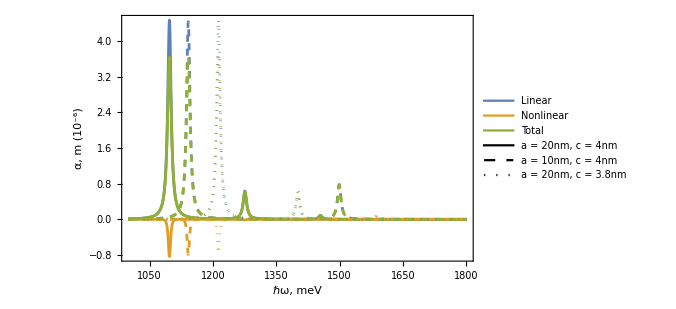

```mathematica
Intensity=5 10^10; (*W/m^2*)
Eω=√(Intensity/(2nr ε0 c0))*10^-6;(*mV/nm*)
Γ=5;(*meV*)

configs={{20,4,0},{10,4,0},{20,3.8,0}};
legend=Column[{LineLegend[colors,{"Linear","Nonlinear","Total"},LabelStyle->{FontFamily->"Times"}],LineLegend[lineStyles,makeLabel@@@configs,LabelStyle->{FontFamily->"Times"}]}];

ωMin=1000;ωMax=1800;  (*meV*)
scaleString="(10^-6)";
scale=10^6;
Plotα1=Plot[
{{scale (Σα1@@torB[configs[[1]]])[ℏω],scale(Σα3@@torB[configs[[1]]])[ℏω],scale(Σα@@torB[configs[[1]]])[ℏω]},{scale (Σα1@@torB[configs[[2]]])[ℏω],scale(Σα3@@torB[configs[[2]]])[ℏω],scale(Σα@@torB[configs[[2]]])[ℏω]},{scale (Σα1@@torB[configs[[3]]])[ℏω],scale(Σα3@@torB[configs[[3]]])[ℏω],scale(Σα@@torB[configs[[3]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
PlotStyle->style,
PlotLegends->legend,
Frame->True,
FrameLabel->{ℏωlabel,αlabel[scaleString]},
ImageSize->500
];
ωMin=50;ωMax=250; (*meV*)
scaleString="(10^-8)";
scale=10^8;
Plotα2=Plot[
{{scale (Σα1@@torB[configs[[1]]])[ℏω],scale(Σα3@@torB[configs[[1]]])[ℏω],scale(Σα@@torB[configs[[1]]])[ℏω]},{scale (Σα1@@torB[configs[[2]]])[ℏω],scale(Σα3@@torB[configs[[2]]])[ℏω],scale(Σα@@torB[configs[[2]]])[ℏω]},{scale (Σα1@@torB[configs[[3]]])[ℏω],scale(Σα3@@torB[configs[[3]]])[ℏω],scale(Σα@@torB[configs[[3]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
PlotStyle->style,
Frame->True,
FrameLabel->{ℏωlabel,αlabel[scaleString]},
ImageSize->250
];
Plotα=Show[
 Plotα1,
 Epilog -> {Inset[Plotα2,Scaled[{0.65,0.65}]]}
]
Export["G:\\My Drive\\Ասպիրանտուրա\\Quantum-Dot\\Graphs\\Absorption.jpeg",Plotα];
```

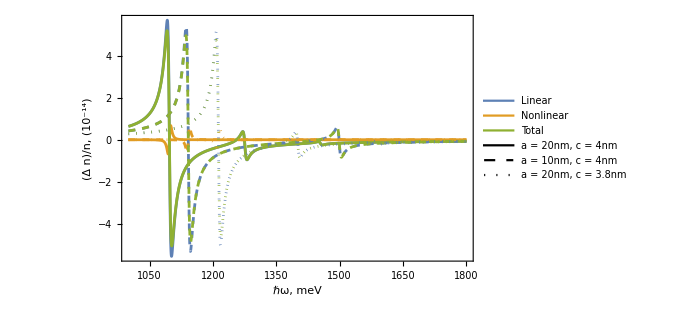

```mathematica
ωMin=1000;ωMax=1800;  (*meV*)
scaleString="(10^-14)";
scale=10^14;
Plotn1=Plot[
{{scale (ΣΔn1@@tonm[configs[[1]]])[ℏω],scale(ΣΔn3@@tonm[configs[[1]]])[ℏω],scale(ΣΔn@@tonm[configs[[1]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[2]]])[ℏω],scale(ΣΔn3@@tonm[configs[[2]]])[ℏω],scale(ΣΔn@@tonm[configs[[2]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[3]]])[ℏω],scale(ΣΔn3@@tonm[configs[[3]]])[ℏω],scale(ΣΔn@@tonm[configs[[3]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
PlotStyle->style,
PlotLegends->legend,
Frame->True,
FrameLabel->{ℏωlabel,nlabel[scaleString]},
ImageSize->500
];
ωMin=50;ωMax=250; (*meV*)
scaleString="(10^-15)";
scale=10^15;
Plotn2=Plot[
{{scale (ΣΔn1@@tonm[configs[[1]]])[ℏω],scale(ΣΔn3@@tonm[configs[[1]]])[ℏω],scale(ΣΔn@@tonm[configs[[1]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[2]]])[ℏω],scale(ΣΔn3@@tonm[configs[[2]]])[ℏω],scale(ΣΔn@@tonm[configs[[2]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[3]]])[ℏω],scale(ΣΔn3@@tonm[configs[[3]]])[ℏω],scale(ΣΔn@@tonm[configs[[3]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
Frame->True,
PlotStyle->style,
FrameLabel->{ℏωlabel,nlabel[scaleString]},
ImageSize->210
];
 Plotn=Show[
 Plotn1,
 Epilog -> {Inset[Plotn2,Scaled[{0.7,0.73}]]}
]
Export["G:\\My Drive\\Ասպիրանտուրա\\Quantum-Dot\\Graphs\\Refractive_index.jpeg",Plotn];
```

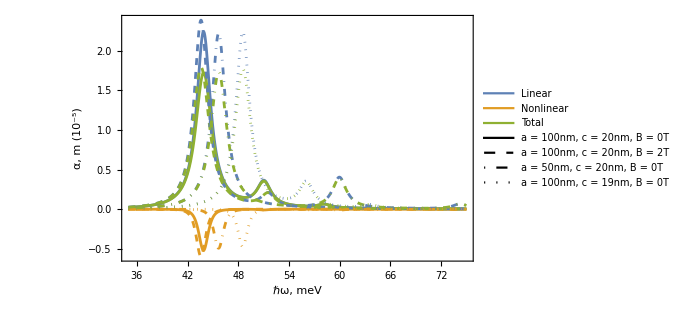

```mathematica
ωMin=35;ωMax=75; (*meV*)
scaleString="(10^-5)";
scale=10^5;
Plotα1=Plot[
{{scale (Σα1@@torB[configs[[1]]])[ℏω],scale(Σα3@@torB[configs[[1]]])[ℏω],scale(Σα@@torB[configs[[1]]])[ℏω]},{scale (Σα1@@torB[configs[[2]]])[ℏω],scale(Σα3@@torB[configs[[2]]])[ℏω],scale(Σα@@torB[configs[[2]]])[ℏω]},{scale (Σα1@@torB[configs[[3]]])[ℏω],scale(Σα3@@torB[configs[[3]]])[ℏω],scale(Σα@@torB[configs[[3]]])[ℏω]},{scale (Σα1@@torB[configs[[4]]])[ℏω],scale(Σα3@@torB[configs[[4]]])[ℏω],scale(Σα@@torB[configs[[4]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
PlotStyle->style,
PlotLegends->legend,
Frame->True,
FrameLabel->{ℏωlabel,αlabel[scaleString]},
ImageSize->500
];
ωMin=0;ωMax=15; (*meV*)
scaleString="(10^-7)";
scale=10^7;
Plotα2=Plot[
{{scale (Σα1@@torB[configs[[1]]])[ℏω],scale(Σα3@@torB[configs[[1]]])[ℏω],scale(Σα@@torB[configs[[1]]])[ℏω]},{scale (Σα1@@torB[configs[[2]]])[ℏω],scale(Σα3@@torB[configs[[2]]])[ℏω],scale(Σα@@torB[configs[[2]]])[ℏω]},{scale (Σα1@@torB[configs[[3]]])[ℏω],scale(Σα3@@torB[configs[[3]]])[ℏω],scale(Σα@@torB[configs[[3]]])[ℏω]},{scale (Σα1@@torB[configs[[4]]])[ℏω],scale(Σα3@@torB[configs[[4]]])[ℏω],scale(Σα@@torB[configs[[4]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
PlotStyle->style,
Frame->True,
FrameLabel->{ℏωlabel,αlabel[scaleString]},
ImageSize->250
];
Plotα=Show[
 Plotα1,
 Epilog -> {Inset[Plotα2,Scaled[{0.65,0.65}]]}
]
Export["G:\\My Drive\\Ասպիրանտուրա\\Quantum-Dot\\Graphs\\Absorption.jpeg",Plotα];
```

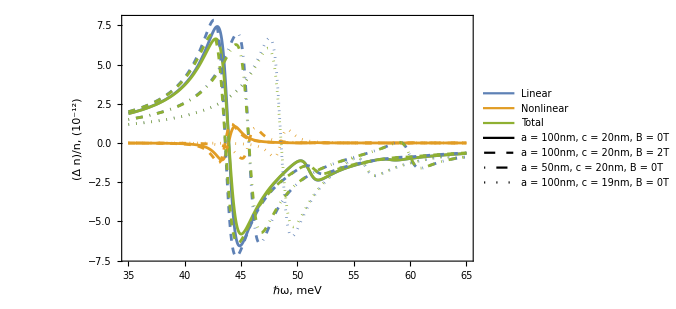

```mathematica
ωMin=35;ωMax=65; (*meV*)
scaleString="(10^-12)";
scale=10^12;
Plotn1=Plot[
{{scale (ΣΔn1@@tonm[configs[[1]]])[ℏω],scale(ΣΔn3@@tonm[configs[[1]]])[ℏω],scale(ΣΔn@@tonm[configs[[1]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[2]]])[ℏω],scale(ΣΔn3@@tonm[configs[[2]]])[ℏω],scale(ΣΔn@@tonm[configs[[2]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[3]]])[ℏω],scale(ΣΔn3@@tonm[configs[[3]]])[ℏω],scale(ΣΔn@@tonm[configs[[3]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[4]]])[ℏω],scale(ΣΔn3@@tonm[configs[[4]]])[ℏω],scale(ΣΔn@@tonm[configs[[4]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
PlotStyle->style,
PlotLegends->legend,
Frame->True,
FrameLabel->{ℏωlabel,nlabel[scaleString]},
ImageSize->500
];
ωMin=0;ωMax=10; (*meV*)
scaleString="(10^-12)";
scale=10^12;
Plotn2=Plot[
{{scale (ΣΔn1@@tonm[configs[[1]]])[ℏω],scale(ΣΔn3@@tonm[configs[[1]]])[ℏω],scale(ΣΔn@@tonm[configs[[1]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[2]]])[ℏω],scale(ΣΔn3@@tonm[configs[[2]]])[ℏω],scale(ΣΔn@@tonm[configs[[2]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[3]]])[ℏω],scale(ΣΔn3@@tonm[configs[[3]]])[ℏω],scale(ΣΔn@@tonm[configs[[3]]])[ℏω]},{scale (ΣΔn1@@tonm[configs[[4]]])[ℏω],scale(ΣΔn3@@tonm[configs[[4]]])[ℏω],scale(ΣΔn@@tonm[configs[[4]]])[ℏω]}},
{ℏω,ωMin,ωMax},
PlotRange->{{ωMin,ωMax},All},
Frame->True,
PlotStyle->style,
FrameLabel->{ℏωlabel,nlabel[scaleString]},
ImageSize->210
];
 Plotn=Show[
 Plotn1,
 Epilog -> {Inset[Plotn2,Scaled[{0.7,0.73}]]}
]
Export["G:\\My Drive\\Ասպիրանտուրա\\Quantum-Dot\\Graphs\\Refractive_index.jpeg",Plotn];
```